```mathematica
x0=0.;
y0=0.;
vx0 =V Cos[th];
vy0=V Sin[th];
vter=Sqrt[m g/ c];

ode1={x''[t] ==  -g (x'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2],y''[t]==  -g (1+  (y'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2] ),x[0]== x0,x'[0]==  vx0, y[0]== y0, y'[0] ==  vy0}/.{V->100,th->50*(Pi/180),m->1,g->9.8,c->0.002};

sol=NDSolve[ode1,{x,y},{t,0,200}];
sol
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

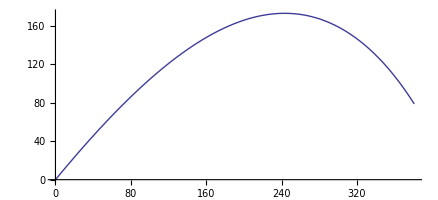

```mathematica
myplot1 = ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,10}];
Show[myplot1]
```

```mathematica
Manipulate[
g=9.8;x0=0.;y0=0.;vx0 =V Cos[th*Pi/180];vy0=V Sin[th*Pi/180];ρair = 1.29 (*kg /(meters^3)*);vter=Sqrt[2 m g/ (c ρair A)];
Module[
{ode1={x''[t] ==  -g (x'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2],y''[t]==  -g (1+  (y'[t] / (vter^2)) Sqrt[(x'[t])^2 + (y'[t])^2] ),x[0]== x0,x'[0]==  vx0, y[0]== y0, y'[0] ==  vy0}

sol=NDSolve[ode1,{x,y},{t,0,200}];},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{700,500}]],
{{V,100,"Initial speed(m/s)"},0,600,Appearance->"Labeled"},{{th,50,"initial angle (degrees)"},0.,90.,Appearance->"Labeled"},
{{m,0,"Projectile mass {kg)"},0.000000001,100.,Appearance->"Labeled"}
{{c,0.5,"Coefficient of quadratic drag"},0.001,10.0,Appearance->"Labeled"}
{{A,0.001,"Projectile cross-section area (m^2)"},0.0000001,50.,Appearance->"Labeled"}]
```